```mathematica
out=Import["Market Maker D Exchange.csv"]
```

{{Tickers,ETF?,Exc Vol April,Exc Vol May,tvol_month,d4,d5,Diff4,Diff5,Volume Bucket,Tick Size,Spread,Price,LogP,SameSide,Middle,PriceRank,Dist,Weights,Volatility,Spread/Tick Size,Rank_Spread_Tick,Rank_Spread_Tick},{FB,0,1,1,716519106,14,10,13,9,10,0.009,0.0132484,26.17,1.4178,1,1,0.611,9.19239,0.00602742,0,1.47205,0.415,0},«6107»,{LSBK,0,6124,6106,5059,5946.5,6073.5,-177.5,-32.5,1,0.03,0.0915,11.25,1.05115,1,1,0.285,-125.511,4.26×10^-8,0,3.05,10,10}}

```mathematica
out=Transpose[out];
```

```mathematica
yy=out[[6]];
yy2=out[[7]];
xx=out[[3]];
xx2=out[[4]];
```

```mathematica
xx=xx[[2;;Length[xx]]];
yy=yy[[2;;Length[yy]]];
xx2=xx2[[2;;Length[xx2]]];
yy2=yy2[[2;;Length[yy2]]];
```

```mathematica
Length[xx2]
Length[yy2]
```

6109

6109

```mathematica
data=Transpose@{xx,yy};
data2=Transpose@{xx2,yy2};
```

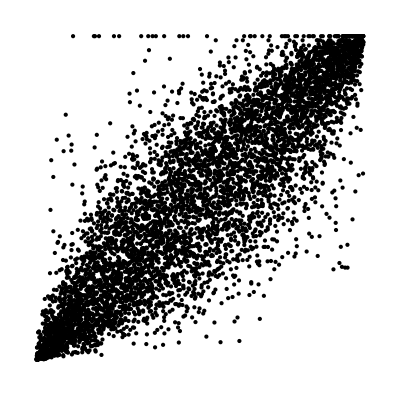

```mathematica
Graphics[Point[data,VertexColors->Hue/@zz]]
```

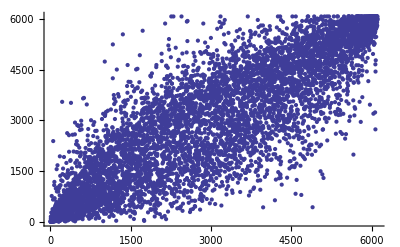

```mathematica
ListPlot[data2]
```

```mathematica
p=Table[ListPlot[data*(1-t)+data2*t,ImageSize->{500,500}],{t,0,1,0.01}];
```

```mathematica
Export["animate.swf",p]
```

animate.swf

```mathematica
ListAnimate[p,13,AnimationRepetitions->3]
```

```mathematica
Export["volume.mov",p,"VideoEncoding"->"MPEG-4 Video","FrameRate"->13]
```

volume.mov